## Forecasting oil prices

The spot prices for Jan 86 - Nov 2003:

```mathematica
spotPrices={22.93,15.45,12.61,12.84,15.38,13.43,11.58,15.1,14.87,14.9,15.22,16.11,18.65,17.75,18.3,18.68,19.44,20.07,21.34,20.31,19.53,19.86,18.85,17.27,17.13,16.8,16.2,17.86,17.42,16.53,15.5,15.52,14.54,13.77,14.14,16.38,18.02,17.94,19.48,21.07,20.12,20.05,19.78,18.58,19.59,20.1,19.86,21.1,22.86,22.11,20.39,18.43,18.2,16.7,18.45,27.31,33.51,36.04,32.33,27.28,25.23,20.48,19.9,20.83,21.23,20.19,21.4,21.69,21.89,23.23,22.46,19.5,18.79,19.01,18.92,20.23,20.98,22.38,21.78,21.34,21.88,21.69,20.34,19.41,19.03,20.09,20.32,20.25,19.95,19.09,17.89,18.01,17.5,18.15,16.61,14.51,15.03,14.78,14.68,16.42,17.89,19.06,19.65,18.38,17.45,17.72,18.07,17.16,18.04,18.57,18.54,19.9,19.74,18.45,17.33,18.02,18.23,17.43,17.99,19.03,18.85,19.09,21.33,23.5,21.17,20.42,21.3,21.9,23.97,24.88,23.71,25.23,25.13,22.18,20.97,19.7,20.82,19.26,19.66,19.95,19.8,21.33,20.19,18.33,16.72,16.06,15.12,15.35,14.91,13.72,14.17,13.47,15.03,14.46,13.,11.35,12.51,12.01,14.68,17.31,17.72,17.92,20.1,21.28,23.8,22.69,25.,26.1,27.26,29.37,29.84,25.72,28.79,31.82,29.7,31.26,33.88,33.11,34.42,28.44,29.59,29.61,27.24,27.49,28.63,27.6,26.42,27.37,26.2,22.17,19.64,19.39,19.71,20.72,24.53,26.18,27.04,25.52,26.97,28.39,29.66,28.84,26.35,29.46,32.95,35.83,33.51,28.17,28.11,30.66,30.75,31.57,28.31,30.34,31.11};
```

```mathematica
Length[spotPrices]
```

215

Smooth a list (universal thresholding at all levels) using the Daubechies filter of length 4:

```mathematica
smoothData[list_]:=InverseWaveletTransform[WaveletThreshold[StationaryWaveletTransform[list,DaubechiesWavelet[2]]]]
```

Take and smooth a sample of size 100 with offest n:

```mathematica
sample[n_]:=smoothData[spotPrices[[n;;n+99]]]
```

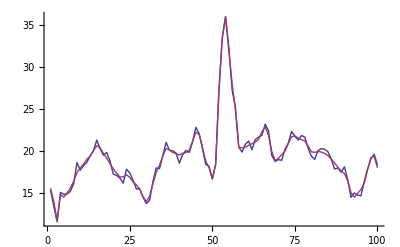

```mathematica
ListPlot[{spotPrices[[5;;104]],sample[5]},Joined->True,PlotRange->All]
```

Forecast the value τ periods in the future from a list. The arguments are the data, how far out to forecast, the filter, and the number of levels:

```mathematica
forecast[data_,τ_,filter_,levels_]:=Module[{sw,rawdwd},(* Compute nondecimated wavelet transform *)sw=StationaryWaveletTransform[data,filter,levels];
(* Get the coefficients *)rawdwd=sw[Automatic];
(* Extrapolate each level *)Do[rawdwd[[i,2]]=ArrayPad[rawdwd[[i,2]],{0,τ},"Extrapolated",InterpolationOrder->3],{i,1,levels+1}];
(* Invert and take the last value *)Last[InverseWaveletTransform[DiscreteWaveletData[rawdwd,filter]]]]
```

### Test example

```mathematica
testData=Table[Sin[1.4 x],{x,0,2 π-(2 π)/128,(2 π)/128}];
```

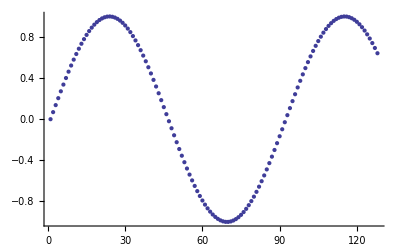

```mathematica
ListPlot[testData]
```

The next point should be

```mathematica
Sin[1.4 2 π]
```

0.587785

Using 1 iteration of Haar:

```mathematica
forecast[testData,1,DaubechiesWavelet[1],1]
```

0.614861

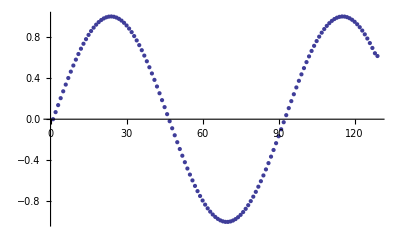

```mathematica
ListPlot[Append[testData,%]]
```

Looking at different length filters and different numbers of iterations:

```mathematica
Grid[Table[forecast[testData,1,DaubechiesWavelet[i],j],{i,1,7},{j,1,5}]]
```

0.614861 | 0.628027 | 0.634202 | 0.636829 | 0.637611
0.624104 | 0.636351 | 0.640433 | 0.641755 | 0.642093
0.629785 | 0.63939 | 0.641514 | 0.641945 | 0.641968
0.633622 | 0.640776 | 0.64183 | 0.641959 | 0.650906
0.636231 | 0.64141 | 0.641919 | 0.641955 | 0.670407
0.638014 | 0.641702 | 0.641944 | 0.641953 | 0.676172
0.639237 | 0.641837 | 0.64195 | 0.642049 | 0.676363

### Oil data

First an example where I’ve modified the routine to save some intermediate results to plot:

```mathematica
forecast2[data_,τ_,filter_,levels_]:=Module[{sw,rawdwd},(* Compute nondecimated wavelet transform *)sw=StationaryWaveletTransform[data,filter,levels];
(* Get the coefficients *)rawdwd=sw[Automatic];
(* Extrapolate each level *)Do[rawdwd[[i,2]]=ArrayPad[rawdwd[[i,2]],{0,τ},"Extrapolated",InterpolationOrder->3],{i,1,levels+1}];
extrapolations=rawdwd;
(* Invert and take the last value *)Last[InverseWaveletTransform[DiscreteWaveletData[rawdwd,filter]]]]
```

Recall sample[n] takes the data points from position n through n+99 and smooths them. Thus the following forecasts the 101th point:

```mathematica
forecast2[sample[1],1,DaubechiesWavelet[7],5]
```

16.5201

```mathematica
spotPrices[[101]]
```

17.89

```mathematica
Map[Length,Table[extrapolations[[i,2]],{i,1,6}]]
```

{101,101,101,101,101,101}

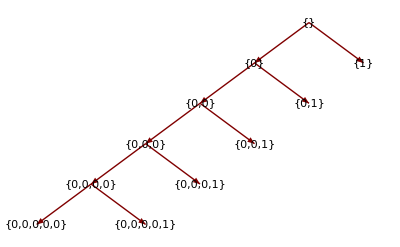

```mathematica
DiscreteWaveletData[extrapolations,DaubechiesWavelet[7]]["TreeView"]
```

The transformed data with the extrapolated point added on:

```mathematica
WaveletListPlot[DiscreteWaveletData[extrapolations,DaubechiesWavelet[7]],Ticks->Full]
```

-Graphics-

Zoom in to check the extrapolations. The last point in each level looks reasonable.

```mathematica
WaveletListPlot[DiscreteWaveletData[extrapolations,DaubechiesWavelet[7]],PlotRange->{{90,101},Automatic},PlotMarkers->Automatic]
```

-Graphics-

Another visualization of the transformation:

```mathematica
WaveletListPlot[DiscreteWaveletData[extrapolations,DaubechiesWavelet[7]],PlotLayout->"CommonYAxis"]
```

-Graphics-

Make 114 predictions using 100 data points (each offset by 1) and compare them to the actual price using 1 iteration of Haar:

```mathematica
results=Table[{spotPrices[[n+100]],forecast[sample[n],1,DaubechiesWavelet[1],1]},{n,1,114}]
```

{{17.89,16.8532},{19.06,19.4425},{19.65,21.3709},{18.38,21.2346},{17.45,16.3085},{17.72,15.9838},{18.07,20.5412},{17.16,16.1023},{18.04,15.3677},{18.57,19.9748},{18.54,17.8789},{19.9,18.5793},{19.74,18.931},{18.45,18.0311},{17.33,18.1569},{18.02,18.8986},{18.23,19.2168},{17.43,19.0713},{17.99,15.0488},{19.03,19.5811},{18.85,18.9844},{19.09,19.6264},{21.33,18.4007},{23.5,24.5727},{21.17,26.8205},{20.42,13.4606},{21.3,21.8077},{21.9,22.1225},{23.97,23.2384},{24.88,27.3345},{23.71,23.9734},{25.23,20.1352},{25.13,29.3858},{22.18,23.444},{20.97,15.1108},{19.7,20.2341},{20.82,19.3789},{19.26,20.2166},{19.66,19.5777},{19.95,20.2684},{19.8,19.6465},{21.33,19.9154},{20.19,20.3553},{18.33,19.2337},{16.72,19.3321},{16.06,16.4593},{15.12,15.0193},{15.35,12.8273},{14.91,13.6331},{13.72,12.4442},{14.17,11.1965},{13.47,15.9092},{15.03,11.7531},{14.46,15.5879},{13.,12.5286},{11.35,10.8267},{12.51,10.4032},{12.01,16.3904},{14.68,10.0346},{17.31,19.2726},{17.72,18.863},{17.92,18.9586},{20.1,19.048},{21.28,20.6182},{23.8,20.9077},{22.69,27.3276},{25.,17.3233},{26.1,27.9233},{27.26,26.7799},{29.37,28.6085},{29.84,32.9228},{25.72,28.2369},{28.79,17.3589},{31.82,38.605},{29.7,30.1617},{31.26,22.6954},{33.88,37.4471},{33.11,36.9781},{34.42,28.5608},{28.44,38.7268},{29.59,18.8193},{29.61,41.5897},{27.24,24.6768},{27.49,20.6351},{28.63,30.7285},{27.6,31.9939},{26.42,24.1365},{27.37,23.6822},{26.2,30.1101},{22.17,26.6771},{19.64,19.8109},{19.39,18.9449},{19.71,19.2405},{20.72,18.1244},{24.53,21.8746},{26.18,30.7528},{27.04,24.1599},{25.52,29.9415},{26.97,22.757},{28.39,31.6945},{29.66,32.7615},{28.84,32.9403},{26.35,29.1504},{29.46,23.2232},{32.95,35.7262},{35.83,36.5551},{33.51,36.2578},{28.17,25.5606},{28.11,27.944},{30.66,31.3357},{30.75,33.6253},{31.57,28.129},{28.31,35.1507},{30.34,18.5322}}

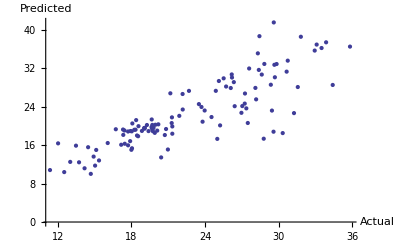

```mathematica
ListPlot[results,AxesLabel->{"Actual","Predicted"}]
```

```mathematica
lm=LinearModelFit[results,x,x]
```

FittedModel[-0.564228+1.02119 x]

```mathematica
lm["RSquared"]
```

0.70719

Repeating with 5 iterations of D7:

```mathematica
results=Table[{spotPrices[[n+100]],forecast[sample[n],1,DaubechiesWavelet[7],5]},{n,1,114}]
```

{{17.89,16.5201},{19.06,17.9363},{19.65,19.3633},{18.38,19.704},{17.45,18.1618},{17.72,17.2824},{18.07,18.0267},{17.16,16.9796},{18.04,16.8015},{18.57,17.9482},{18.54,17.7795},{19.9,18.2001},{19.74,18.456},{18.45,18.7842},{17.33,18.3075},{18.02,17.8765},{18.23,18.0774},{17.43,18.6232},{17.99,17.4682},{19.03,18.6235},{18.85,18.7178},{19.09,19.2463},{21.33,18.8066},{23.5,21.61},{21.17,24.1064},{20.42,21.562},{21.3,20.7681},{21.9,21.3798},{23.97,22.8906},{24.88,24.9934},{23.71,25.7633},{25.23,24.3842},{25.13,25.8956},{22.18,25.6079},{20.97,22.5211},{19.7,21.278},{20.82,20.082},{19.26,20.8193},{19.66,20.337},{19.95,20.3337},{19.8,20.0647},{21.33,20.0602},{20.19,20.4565},{18.33,20.2135},{16.72,19.7147},{16.06,17.6967},{15.12,16.4491},{15.35,15.1485},{14.91,15.1483},{13.72,14.3279},{14.17,13.0583},{13.47,13.7035},{15.03,12.0934},{14.46,13.0925},{13.,12.7238},{11.35,11.423},{12.51,9.85007},{12.01,10.9966},{14.68,10.8492},{17.31,13.592},{17.72,16.6033},{17.92,17.5438},{20.1,17.3715},{21.28,18.5577},{23.8,19.7862},{22.69,23.1238},{25.,21.7066},{26.1,24.1968},{27.26,25.9838},{29.37,26.9933},{29.84,29.5222},{25.72,29.9815},{28.79,25.9128},{31.82,29.2324},{29.7,32.323},{31.26,30.2169},{33.88,31.8098},{33.11,34.8657},{34.42,34.0914},{28.44,35.7506},{29.59,30.2697},{29.61,31.047},{27.24,31.1908},{27.49,28.1489},{28.63,29.2532},{27.6,30.2112},{26.42,28.9102},{27.37,27.402},{26.2,28.5661},{22.17,27.8619},{19.64,23.9512},{19.39,21.4036},{19.71,20.3636},{20.72,20.0362},{24.53,21.368},{26.18,25.3536},{27.04,26.538},{25.52,27.7919},{26.97,26.2322},{28.39,27.4633},{29.66,29.0442},{28.84,30.2802},{26.35,29.2375},{29.46,26.5943},{32.95,29.6719},{35.83,33.8512},{33.51,36.2457},{28.17,34.0778},{28.11,28.9195},{30.66,28.9611},{30.75,31.6375},{31.57,31.7382},{28.31,32.6699},{30.34,28.5729}}

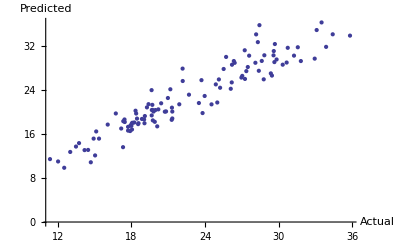

```mathematica
ListPlot[results,AxesLabel->{"Actual","Predicted"}]
```

```mathematica
lm=LinearModelFit[results,x,x]
```

FittedModel[-0.562209+1.029 x]

```mathematica
lm["RSquared"]
```

0.890135

Repeating previous without denoising:

```mathematica
results=Table[{spotPrices[[n+100]],forecast[spotPrices[[n;;n+99]],1,DaubechiesWavelet[7],5]},{n,1,114}]
```

{{17.89,16.6364},{19.06,18.1143},{19.65,19.2401},{18.38,19.7896},{17.45,18.5034},{17.72,17.561},{18.07,17.7963},{17.16,18.0891},{18.04,17.1274},{18.57,17.9373},{18.54,18.3868},{19.9,18.2878},{19.74,19.5977},{18.45,19.4204},{17.33,18.142},{18.02,17.063},{18.23,17.8095},{17.43,18.1004},{17.99,17.3968},{19.03,18.053},{18.85,19.1802},{19.09,19.0935},{21.33,19.4248},{23.5,21.7545},{21.17,24.0279},{20.42,21.8231},{21.3,21.1969},{21.9,22.1765},{23.97,22.8507},{24.88,24.948},{23.71,25.847},{25.23,24.6357},{25.13,26.0824},{22.18,25.8949},{20.97,22.8626},{19.7,21.5756},{20.82,20.2386},{19.26,21.2798},{19.66,19.6515},{19.95,19.9935},{19.8,20.2423},{21.33,20.0657},{20.19,21.5795},{18.33,20.4411},{16.72,18.5911},{16.06,16.9714},{15.12,16.2562},{15.35,15.2004},{14.91,15.2371},{13.72,14.549},{14.17,13.0515},{13.47,13.1751},{15.03,12.1766},{14.46,13.515},{13.,12.8371},{11.35,11.3965},{12.51,9.88564},{12.01,11.2067},{14.68,10.8402},{17.31,13.572},{17.72,16.2169},{17.92,16.6344},{20.1,16.8476},{21.28,19.0747},{23.8,20.3425},{22.69,22.997},{25.,22.0499},{26.1,24.5358},{27.26,25.8138},{29.37,27.1489},{29.84,29.4138},{25.72,30.0306},{28.79,26.0379},{31.82,29.2004},{29.7,32.3221},{31.26,30.3209},{33.88,32.0051},{33.11,34.7628},{34.42,34.1365},{28.44,35.5888},{29.59,29.7497},{29.61,31.0089},{27.24,31.1045},{27.49,28.7783},{28.63,29.031},{27.6,30.1685},{26.42,29.1374},{27.37,27.9541},{26.2,28.8975},{22.17,27.7124},{19.64,23.6591},{19.39,21.0804},{19.71,20.7156},{20.72,20.9006},{24.53,21.7297},{26.18,25.3313},{27.04,26.8025},{25.52,27.5376},{26.97,25.9485},{28.39,27.3795},{29.66,28.8337},{28.84,30.1647},{26.35,29.4241},{29.46,27.0053},{32.95,30.1388},{35.83,33.6395},{33.51,36.5486},{28.17,34.2972},{28.11,29.0429},{30.66,29.0603},{30.75,31.6579},{31.57,31.8016},{28.31,32.6701},{30.34,29.4454}}

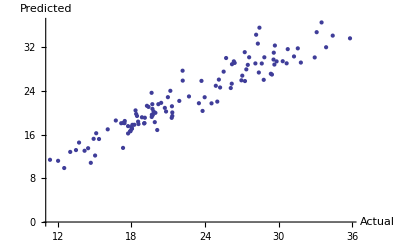

```mathematica
ListPlot[results,AxesLabel->{"Actual","Predicted"}]
```

```mathematica
lm=LinearModelFit[results,x,x]
```

FittedModel[-0.601642+1.03426 x]

```mathematica
lm["RSquared"]
```

0.895721

### Comparison: Using the last data point as a predictor

```mathematica
results=Table[{spotPrices[[n+100]],spotPrices[[n+99]]},{n,1,114}]
```

{{17.89,16.42},{19.06,17.89},{19.65,19.06},{18.38,19.65},{17.45,18.38},{17.72,17.45},{18.07,17.72},{17.16,18.07},{18.04,17.16},{18.57,18.04},{18.54,18.57},{19.9,18.54},{19.74,19.9},{18.45,19.74},{17.33,18.45},{18.02,17.33},{18.23,18.02},{17.43,18.23},{17.99,17.43},{19.03,17.99},{18.85,19.03},{19.09,18.85},{21.33,19.09},{23.5,21.33},{21.17,23.5},{20.42,21.17},{21.3,20.42},{21.9,21.3},{23.97,21.9},{24.88,23.97},{23.71,24.88},{25.23,23.71},{25.13,25.23},{22.18,25.13},{20.97,22.18},{19.7,20.97},{20.82,19.7},{19.26,20.82},{19.66,19.26},{19.95,19.66},{19.8,19.95},{21.33,19.8},{20.19,21.33},{18.33,20.19},{16.72,18.33},{16.06,16.72},{15.12,16.06},{15.35,15.12},{14.91,15.35},{13.72,14.91},{14.17,13.72},{13.47,14.17},{15.03,13.47},{14.46,15.03},{13.,14.46},{11.35,13.},{12.51,11.35},{12.01,12.51},{14.68,12.01},{17.31,14.68},{17.72,17.31},{17.92,17.72},{20.1,17.92},{21.28,20.1},{23.8,21.28},{22.69,23.8},{25.,22.69},{26.1,25.},{27.26,26.1},{29.37,27.26},{29.84,29.37},{25.72,29.84},{28.79,25.72},{31.82,28.79},{29.7,31.82},{31.26,29.7},{33.88,31.26},{33.11,33.88},{34.42,33.11},{28.44,34.42},{29.59,28.44},{29.61,29.59},{27.24,29.61},{27.49,27.24},{28.63,27.49},{27.6,28.63},{26.42,27.6},{27.37,26.42},{26.2,27.37},{22.17,26.2},{19.64,22.17},{19.39,19.64},{19.71,19.39},{20.72,19.71},{24.53,20.72},{26.18,24.53},{27.04,26.18},{25.52,27.04},{26.97,25.52},{28.39,26.97},{29.66,28.39},{28.84,29.66},{26.35,28.84},{29.46,26.35},{32.95,29.46},{35.83,32.95},{33.51,35.83},{28.17,33.51},{28.11,28.17},{30.66,28.11},{30.75,30.66},{31.57,30.75},{28.31,31.57},{30.34,28.31}}

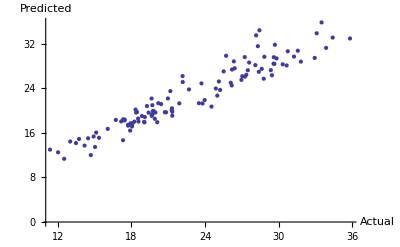

```mathematica
ListPlot[results,AxesLabel->{"Actual","Predicted"}]
```

```mathematica
lm=LinearModelFit[results,x,x]
```

FittedModel[1.02215+0.949486 x]

```mathematica
lm["RSquared"]
```

0.906766

### Comparison: Using the last smoothed data point as a predictor

```mathematica
results=Table[{spotPrices[[n+100]],Last[sample[n]]},{n,1,114}]
```

{{17.89,16.2953},{19.06,17.706},{19.65,19.1748},{18.38,19.5609},{17.45,18.0348},{17.72,17.1694},{18.07,17.9568},{17.16,16.9666},{18.04,16.8421},{18.57,18.0577},{18.54,17.9649},{19.9,18.4645},{19.74,18.7624},{18.45,19.1066},{17.33,18.621},{18.02,18.1555},{18.23,18.2929},{17.43,18.7587},{17.99,17.501},{19.03,18.5611},{18.85,18.5666},{19.09,19.0158},{21.33,18.4846},{23.5,21.1941},{21.17,23.5946},{20.42,20.9081},{21.3,20.0006},{21.9,20.5115},{23.97,21.9457},{24.88,24.0233},{23.71,24.7966},{25.23,23.4583},{25.13,25.0381},{22.18,24.8391},{20.97,21.835},{19.7,20.6702},{20.82,19.5385},{19.26,20.3716},{19.66,19.9552},{19.95,20.0088},{19.8,19.7792},{21.33,19.7972},{20.19,20.2072},{18.33,19.9589},{16.72,19.4504},{16.06,17.4366},{15.12,16.2608},{15.35,15.0763},{14.91,15.2625},{13.72,14.6909},{14.17,13.7214},{13.47,14.6932},{15.03,13.379},{14.46,14.5984},{13.,14.3442},{11.35,13.0189},{12.51,11.3095},{12.01,12.2934},{14.68,12.0156},{17.31,14.6907},{17.72,17.6873},{17.92,18.6249},{20.1,18.4454},{21.28,19.59},{23.8,20.7287},{22.69,23.9259},{25.,22.3516},{26.1,24.6624},{27.26,26.2715},{29.37,27.1156},{29.84,29.4811},{25.72,29.7916},{28.79,25.5967},{31.82,28.8262},{29.7,31.819},{31.26,29.5912},{33.88,31.0589},{33.11,33.9846},{34.42,33.0551},{28.44,34.5815},{29.59,28.9619},{29.61,29.6254},{27.24,29.6921},{27.49,26.6111},{28.63,27.7096},{27.6,28.684},{26.42,27.3768},{27.37,25.8696},{26.2,27.0284},{22.17,26.3452},{19.64,22.4589},{19.39,19.9685},{19.71,19.0432},{20.72,18.852},{24.53,20.3645},{26.18,24.5417},{27.04,25.8986},{25.52,27.2741},{26.97,25.7804},{28.39,27.055},{29.66,28.6139},{28.84,29.7797},{26.35,28.6439},{29.46,25.9386},{32.95,28.9817},{35.83,33.1599},{33.51,35.5217},{28.17,33.2952},{28.11,28.0648},{30.66,28.0244},{30.75,30.6446},{31.57,30.6984},{28.31,31.5807},{30.34,27.4452}}

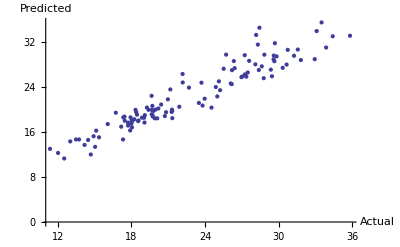

```mathematica
ListPlot[results,AxesLabel->{"Actual","Predicted"}]
```

```mathematica
lm=LinearModelFit[results,x,x]
```

FittedModel[1.06119+0.94428 x]

```mathematica
lm["RSquared"]
```

0.899449

### Comparison: Using the futures contract as a predictor

```mathematica
futuresPrices={22.98,15.46,12.62,12.75,15.26,13.38,11.58,15.11,14.94,14.89,15.23,16.09,18.67,17.73,18.28,18.6,19.33,19.99,21.33,20.23,19.52,19.86,18.85,17.26,17.15,16.76,16.21,17.88,17.45,16.56,15.51,15.53,14.46,13.8,13.98,16.28,17.98,17.82,19.44,20.94,20.03,19.99,19.66,18.55,19.59,20.1,19.83,21.09,22.64,22.11,20.41,18.58,18.46,16.86,18.64,27.18,33.69,35.92,32.3,27.16,24.7,20.54,19.88,20.82,21.25,20.2,21.43,21.68,21.86,23.23,22.43,19.53,18.82,19.01,18.95,20.26,21.,22.36,21.74,21.29,21.92,21.71,20.36,19.41,19.07,20.08,20.35,20.33,19.98,19.13,17.9,18.01,17.52,18.17,16.74,14.53,15.02,14.78,14.65,16.33,17.83,19.07,19.66,18.38,17.47,17.71,18.1,17.16,17.99,18.53,18.55,19.89,19.74,18.4,17.26,17.81,18.21,17.4,18.,19.04,18.7,18.78,21.18,23.3,21.09,20.43,21.25,21.91,23.93,24.9,23.55,25.12,25.18,22.17,20.97,19.73,20.87,19.22,19.66,19.95,19.78,21.28,20.22,18.32,16.73,16.08,15.04,15.46,14.93,13.67,14.09,13.38,14.97,14.42,13.04,11.31,12.49,12.02,14.68,17.3,17.77,17.92,20.1,21.28,23.79,22.67,24.77,26.09,27.01,29.3,29.89,25.54,28.81,31.53,29.72,31.14,33.87,32.93,34.26,28.4,29.26,29.64,27.27,27.62,28.68,27.59,26.47,27.31,25.69,22.21,19.67,19.4,19.73,20.76,24.44,26.26,26.95,25.55,26.94,28.2,29.67,28.86,26.19,29.39,32.7,35.73,33.16,28.14,28.07,30.52,30.7,31.6,28.31,30.35,31.06};
```

```mathematica
Length[spotPrices]
Length[futuresPrices]
```

215

215

```mathematica
results=Table[{spotPrices[[n+100]],futuresPrices[[n+99]]},{n,1,114}]
```

{{17.89,16.33},{19.06,17.83},{19.65,19.07},{18.38,19.66},{17.45,18.38},{17.72,17.47},{18.07,17.71},{17.16,18.1},{18.04,17.16},{18.57,17.99},{18.54,18.53},{19.9,18.55},{19.74,19.89},{18.45,19.74},{17.33,18.4},{18.02,17.26},{18.23,17.81},{17.43,18.21},{17.99,17.4},{19.03,18.},{18.85,19.04},{19.09,18.7},{21.33,18.78},{23.5,21.18},{21.17,23.3},{20.42,21.09},{21.3,20.43},{21.9,21.25},{23.97,21.91},{24.88,23.93},{23.71,24.9},{25.23,23.55},{25.13,25.12},{22.18,25.18},{20.97,22.17},{19.7,20.97},{20.82,19.73},{19.26,20.87},{19.66,19.22},{19.95,19.66},{19.8,19.95},{21.33,19.78},{20.19,21.28},{18.33,20.22},{16.72,18.32},{16.06,16.73},{15.12,16.08},{15.35,15.04},{14.91,15.46},{13.72,14.93},{14.17,13.67},{13.47,14.09},{15.03,13.38},{14.46,14.97},{13.,14.42},{11.35,13.04},{12.51,11.31},{12.01,12.49},{14.68,12.02},{17.31,14.68},{17.72,17.3},{17.92,17.77},{20.1,17.92},{21.28,20.1},{23.8,21.28},{22.69,23.79},{25.,22.67},{26.1,24.77},{27.26,26.09},{29.37,27.01},{29.84,29.3},{25.72,29.89},{28.79,25.54},{31.82,28.81},{29.7,31.53},{31.26,29.72},{33.88,31.14},{33.11,33.87},{34.42,32.93},{28.44,34.26},{29.59,28.4},{29.61,29.26},{27.24,29.64},{27.49,27.27},{28.63,27.62},{27.6,28.68},{26.42,27.59},{27.37,26.47},{26.2,27.31},{22.17,25.69},{19.64,22.21},{19.39,19.67},{19.71,19.4},{20.72,19.73},{24.53,20.76},{26.18,24.44},{27.04,26.26},{25.52,26.95},{26.97,25.55},{28.39,26.94},{29.66,28.2},{28.84,29.67},{26.35,28.86},{29.46,26.19},{32.95,29.39},{35.83,32.7},{33.51,35.73},{28.17,33.16},{28.11,28.14},{30.66,28.07},{30.75,30.52},{31.57,30.7},{28.31,31.6},{30.34,28.31}}

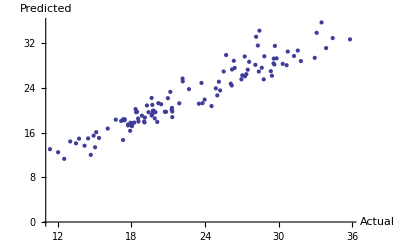

```mathematica
ListPlot[results,AxesLabel->{"Actual","Predicted"}]
```

```mathematica
lm=LinearModelFit[results,x,x]
```

FittedModel[1.08298+0.944744 x]

```mathematica
lm["RSquared"]
```

0.906597

### Comparison: Just extrapolate original data

```mathematica
results=Table[{spotPrices[[n+100]],Last[ArrayPad[spotPrices[[n;;n+99]],{0,1},"Extrapolated",InterpolationOrder->3]]},{n,1,114}]
```

{{17.89,21.69},{19.06,16.98},{19.65,19.9},{18.38,19.38},{17.45,13.97},{17.72,19.06},{18.07,20.05},{17.16,17.38},{18.04,13.65},{18.57,23.76},{18.54,16.61},{19.9,17.74},{19.74,24.6},{18.45,15.15},{17.33,16.42},{18.02,17.68},{18.23,22.16},{17.43,15.67},{17.99,15.09},{19.03,22.28},{18.85,19.67},{19.09,15.75},{21.33,21.39},{23.5,27.15},{21.17,23.53},{20.42,9.91},{21.3,27.33},{21.9,23.86},{23.97,20.31},{24.88,29.26},{23.71,22.},{25.23,19.54},{25.13,34.21},{22.18,19.1},{20.97,15.15},{19.7,26.09},{20.82,16.57},{19.26,26.78},{19.66,9.95},{19.95,26.66},{19.8,18.06},{21.33,18.88},{20.19,26.66},{18.33,12.03},{16.72,17.7},{16.06,16.33},{15.12,17.05},{15.35,12.67},{14.91,18.2},{13.72,11.96},{14.17,11.7},{13.47,18.65},{15.03,8.83},{14.46,22.26},{13.,7.37},{11.35,11.89},{12.51,10.21},{12.01,19.48},{14.68,5.38},{17.31,25.35},{17.72,16.69},{17.92,13.73},{20.1,19.92},{21.28,26.45},{23.8,18.48},{22.69,30.},{25.,12.98},{26.1,37.78},{27.26,21.36},{29.37,29.75},{29.84,33.32},{25.72,26.08},{28.79,14.06},{31.82,50.83},{29.7,27.58},{31.26,17.32},{33.88,45.33},{33.11,34.94},{34.42,24.5},{28.44,43.28},{29.59,5.8},{29.61,52.29},{27.24,20.24},{27.49,21.22},{28.63,35.37},{27.6,28.93},{26.42,21.34},{27.37,27.11},{26.2,32.73},{22.17,18.66},{19.64,14.54},{19.39,22.97},{19.71,22.2},{20.72,18.89},{24.53,22.54},{26.18,33.25},{27.04,20.71},{25.52,28.48},{26.97,20.03},{28.39,36.74},{29.66,26.78},{28.84,30.66},{26.35,23.99},{29.46,22.61},{32.95,45.44},{35.83,31.6},{33.51,37.11},{28.17,21.4},{28.11,21.99},{30.66,41.63},{30.75,33.15},{31.57,23.31},{28.31,36.31},{30.34,16.16}}

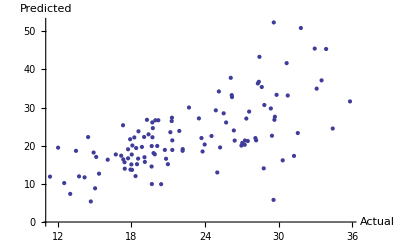

```mathematica
ListPlot[results,AxesLabel->{"Actual","Predicted"}]
```

```mathematica
lm=LinearModelFit[results,x,x]
```

FittedModel[-0.329987+1.01159 x]

```mathematica
lm["RSquared"]
```

0.421684

Repeat with smoothed data:

```mathematica
results=Table[{spotPrices[[n+100]],Last[ArrayPad[sample[n],{0,1},"Extrapolated",InterpolationOrder->3]]},{n,1,114}]
```

{{17.89,17.4112},{19.06,21.179},{19.65,23.5669},{18.38,22.9083},{17.45,14.5822},{17.72,14.7982},{18.07,23.1257},{17.16,15.2381},{18.04,13.8933},{18.57,21.892},{18.54,17.7929},{19.9,18.694},{19.74,19.0996},{18.45,16.9556},{17.33,17.6927},{18.02,19.6416},{18.23,20.1407},{17.43,19.3839},{17.99,12.5966},{19.03,20.601},{18.85,19.4023},{19.09,20.2369},{21.33,18.3168},{23.5,27.9512},{21.17,30.0464},{20.42,6.01311},{21.3,23.6148},{21.9,23.7334},{23.97,24.5311},{24.88,30.6458},{23.71,23.1501},{25.23,16.8122},{25.13,33.7335},{22.18,22.049},{20.97,8.38654},{19.7,19.798},{20.82,19.2193},{19.26,20.0616},{19.66,19.2002},{19.95,20.528},{19.8,19.5139},{21.33,20.0336},{20.19,20.5034},{18.33,18.5086},{16.72,19.2137},{16.06,15.482},{15.12,13.7779},{15.35,10.5783},{14.91,12.0037},{13.72,10.1975},{14.17,8.67152},{13.47,17.1252},{15.03,10.1271},{14.46,16.5773},{13.,10.713},{11.35,8.63449},{12.51,9.49682},{12.01,20.4875},{14.68,8.05366},{17.31,23.8545},{17.72,20.0386},{17.92,19.2924},{20.1,19.6505},{21.28,21.6464},{23.8,21.0866},{22.69,30.7293},{25.,12.295},{26.1,31.1841},{27.26,27.2884},{29.37,30.1014},{29.84,36.3646},{25.72,26.6822},{28.79,9.12103},{31.82,48.3839},{29.7,28.5045},{31.26,15.7996},{33.88,43.8354},{33.11,39.9715},{34.42,24.0666},{28.44,42.8722},{29.59,8.6767},{29.61,53.554},{27.24,19.6615},{27.49,14.659},{28.63,33.7475},{27.6,35.3037},{26.42,20.8963},{27.37,21.4949},{26.2,33.1917},{22.17,27.009},{19.64,17.1629},{19.39,17.9212},{19.71,19.4378},{20.72,17.3968},{24.53,23.3846},{26.18,36.9638},{27.04,22.4213},{25.52,32.6088},{26.97,19.7336},{28.39,36.3339},{29.66,36.9091},{28.84,36.1009},{26.35,29.657},{29.46,20.5078},{32.95,42.4706},{35.83,39.9503},{33.51,36.994},{28.17,17.826},{28.11,27.8233},{30.66,34.6471},{30.75,36.6061},{31.57,25.5596},{28.31,38.7208},{30.34,9.61916}}

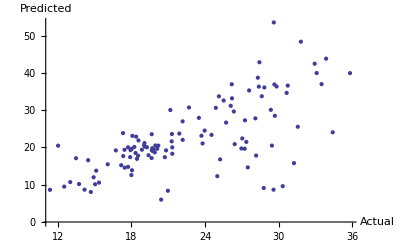

```mathematica
ListPlot[results,AxesLabel->{"Actual","Predicted"}]
```

```mathematica
lm=LinearModelFit[results,x,x]
```

FittedModel[-2.18964+1.0981 x]

```mathematica
lm["RSquared"]
```

0.450027

### Possible next steps

1) Make sure I understand what ArrayPad does.
2) Try other ways to extrapolate the levels.
3) Try different amounts of smoothing.
4) Try other data sets. In general what are the characteristics of a data set where wavelets would outperform other methods?
5) More literature search on forecasting with wavelets.
6) Browse books on time series to get a better feel for the big picture.